# tapered fiber mirror focus scans

P. Huft

Analysis of data from raster scanning a tapered fiber as a point detector to map out the 0.6 NA parabolic mirror focus.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## 2022.11.02

### large range low res 3D scan

I turned the tube 90 degrees about its axis so that the slot which previously faced toward the front of the clean box now faces up. This was to deduce whether the apparent aberrations were from the fiber’s collection modes. The fiber needed to be slid out of the tube before rotating the tube, but it was kept in the same orientation roughly by marking the rod it was mounted to and the mount so there was an alignment reference.

```mathematica
files={
"0-2022-11-02-14-23-xStepSize1.00-yzStepSize0.30-xStart9.28.txt",
"1-2022-11-02-14-24-xStepSize1.00-yzStepSize0.30-xStart9.28.txt","2-2022-11-02-14-25-xStepSize1.00-yzStepSize0.30-xStart9.28.txt","3-2022-11-02-14-26-xStepSize1.00-yzStepSize0.30-xStart9.28.txt","4-2022-11-02-14-27-xStepSize1.00-yzStepSize0.30-xStart9.28.txt","5-2022-11-02-14-28-xStepSize1.00-yzStepSize0.30-xStart9.28.txt","6-2022-11-02-14-29-xStepSize1.00-yzStepSize0.30-xStart9.28.txt","7-2022-11-02-14-31-xStepSize1.00-yzStepSize0.30-xStart9.28.txt","8-2022-11-02-14-32-xStepSize1.00-yzStepSize0.30-xStart9.28.txt",
"9-2022-11-02-14-33-xStepSize1.00-yzStepSize0.30-xStart9.28.txt",
"10-2022-11-02-14-34-xStepSize1.00-yzStepSize0.30-xStart9.28.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
maxima=Array[Max[slices[[#]]]&,Length[slices]];
maxIdx=SortBy[Transpose@{Range[len],maxima},#[[2]]&][[-1,1]];
slices-=Min[slices[[maxIdx]]];
slices/=Max[slices[[maxIdx]]];
{xdim,ydim}=Dimensions[slices[[1]]]
data=slices;
len=Length[data];
Array[(data[[#,3,3;;8]]=1)&,len];
imageTable=Array[Image[data[[#,;;,;;]]]&,len];
GraphicsRow[imageTable]
"peak value in each frame"
Array[Max[slices[[#]]]&,Length[slices]]
```

{34,34}

-Graphics-

peak value in each frame

{0.180783,0.257281,0.459941,0.517357,0.79739,1.,0.833398,0.636841,0.471501,0.357195,0.268979}

### high res in-focus transverse scan

```mathematica
files={
"0-2022-11-02-14-41-xStepSize1.00-yzStepSize0.20-xStart14.06.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
```

```mathematica
Image[normslices[[1]]]
```

-Graphics-

## 2022.11.01

### Three 3D scans - 852, 780, and both at the same time.

Scans with 780 and 852 combined into a forked fiber. I alternated between either wavelength and both. The power coupled into the fiber was tuned to give approximately the same coupling efficiency into the tapered fiber by looking at the APD signal near the focus.

Scans with both 780 and 852:

```mathematica
files={
"852and780_0-2022-11-01-11-16-xStepSize0.50-yzStepSize0.20.txt",
"852and780_1-2022-11-01-11-17-xStepSize0.50-yzStepSize0.20.txt",
"852and780_2-2022-11-01-11-18-xStepSize0.50-yzStepSize0.20.txt",
"852and780_3-2022-11-01-11-19-xStepSize0.50-yzStepSize0.20.txt",
"852and780_4-2022-11-01-11-20-xStepSize0.50-yzStepSize0.20.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
slices-=Min[slices[[3]]];
slices/=Max[slices[[3]]];
{xdim,ydim}=Dimensions[slices[[1]]]
data=slices;
len=Length[data];
Array[(data[[#,3,3;;8]]=1)&,len];
imageTable=Array[Image[data[[#,;;,;;]]]&,len];
GraphicsRow[imageTable]
"peak value in each frame"
Array[Max[slices[[#]]]&,Length[slices]]
```

{31,31}

-Graphics-

peak value in each frame

{0.841211,0.880916,1.,0.897535,0.78623}

```mathematica
imageTable[[3]]
```

-Graphics-

{w→1.01794,x0→3.12401}

{w→0.669755,x0→2.63133}

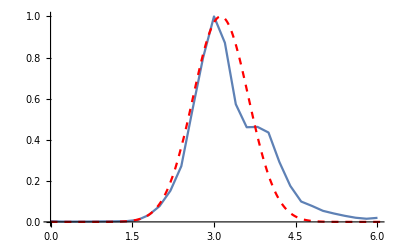

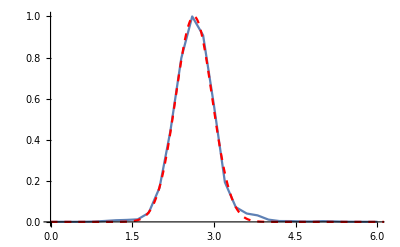

```mathematica
focus=slices[[3]];
xdata=Transpose@{Range[0,(xdim-1)*0.2,0.2],focus[[14,;;]]};
ydata=Transpose@{Range[0,(ydim-1)*0.2,0.2],focus[[;;,16]]};
model=Exp[-(2(x-x0)^2)/w^2];
xfit=FindFit[xdata,model,{{w,0.6},{x0,3}},x]
yfit=FindFit[ydata,model,{{w,0.6},{x0,3.5}},x]
Show[ListPlot[xdata,PlotRange->All,Joined->True(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],
Plot[model/.xfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
Show[ListPlot[ydata,PlotRange->All,Joined->True(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],Plot[model/.yfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
```

Scan with only 780.

```mathematica
files={
"0-2022-11-01-11-22-xStepSize0.50-yzStepSize0.20.txt",
"1-2022-11-01-11-23-xStepSize0.50-yzStepSize0.20.txt",
"2-2022-11-01-11-24-xStepSize0.50-yzStepSize0.20.txt",
"3-2022-11-01-11-25-xStepSize0.50-yzStepSize0.20.txt",
"4-2022-11-01-11-26-xStepSize0.50-yzStepSize0.20.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
slices-=Min[slices[[2]]];
norm780=Max[slices[[2]]];
slices/=norm780;
{xdim,ydim}=Dimensions[slices[[1]]]
data=slices;
len=Length[data];
Array[(data[[#,3,3;;8]]=1)&,len];
imageTable=Array[Image[data[[#,;;,;;]]]&,len];
GraphicsRow[imageTable]
"peak value in each frame"
Array[Max[slices[[#]]]&,Length[slices]]
```

{31,31}

-Graphics-

peak value in each frame

{0.85564,1.,0.981261,0.905857,0.771804}

```mathematica
imageTable[[2]]
```

-Graphics-

{w→0.896497,x0→3.08645}

{w→0.670262,x0→2.45981}

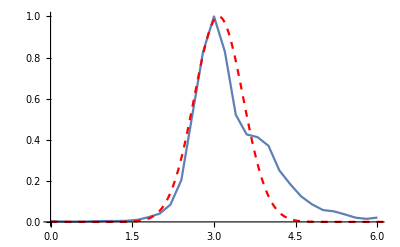

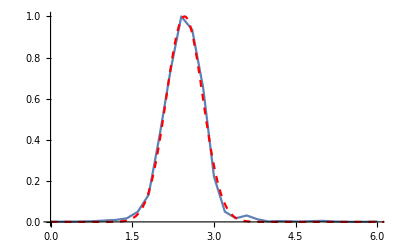

```mathematica
focus=slices[[2]];
xdata=Transpose@{Range[0,(xdim-1)*0.2,0.2],focus[[13,;;]]};
ydata=Transpose@{Range[0,(ydim-1)*0.2,0.2],focus[[;;,16]]};
model=Exp[-(2(x-x0)^2)/w^2];
xfit=FindFit[xdata,model,{{w,0.6},{x0,3}},x]
yfit=FindFit[ydata,model,{{w,0.6},{x0,2.5}},x]
Show[ListPlot[xdata,PlotRange->All,Joined->True(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],
Plot[model/.xfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
Show[ListPlot[ydata,PlotRange->All,Joined->True(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],Plot[model/.yfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
```

Scan with only 852, normalized to slice 2 of the 780 data.

```mathematica
files={
"852_0-2022-11-01-11-28-xStepSize0.50-yzStepSize0.20.txt",
"852_1-2022-11-01-11-29-xStepSize0.50-yzStepSize0.20.txt",
"852_2-2022-11-01-11-30-xStepSize0.50-yzStepSize0.20.txt",
"852_3-2022-11-01-11-31-xStepSize0.50-yzStepSize0.20.txt",
"852_4-2022-11-01-11-32-xStepSize0.50-yzStepSize0.20.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
slices-=Min[slices[[2]]];
slices/=norm780;
{xdim,ydim}=Dimensions[slices[[1]]]
data=normslices;
len=Length[data];
Array[(data[[#,3,3;;8]]=1)&,len];
imageTable=Array[Image[data[[#,;;,;;]]]&,len];
GraphicsRow[imageTable]
"peak value in each frame"
Array[Max[slices[[#]]]&,Length[slices]]
```

{31,31}

-Graphics-

peak value in each frame

{0.402056,0.418661,0.4079,0.378874,0.310424}

```mathematica
imageTable[[2]]
```

-Graphics-

{w→1.21764,x0→3.39426}

{w→0.712761,x0→2.27215}

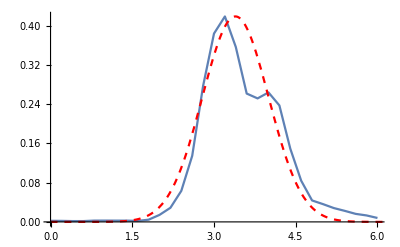

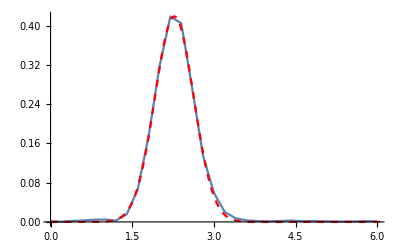

```mathematica
focus=slices[[2]];
xdata=Transpose@{Range[0,(xdim-1)*0.2,0.2],focus[[12,;;]]};
ydata=Transpose@{Range[0,(ydim-1)*0.2,0.2],focus[[;;,17]]};
model=Max[focus]Exp[-(2(x-x0)^2)/w^2];
xfit=FindFit[xdata,model,{{w,0.6},{x0,3}},x]
yfit=FindFit[ydata,model,{{w,0.6},{x0,2.5}},x]
Show[ListPlot[xdata,PlotRange->All,Joined->True(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],
Plot[model/.xfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
Show[ListPlot[ydata,PlotRange->All,Joined->True(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],Plot[model/.yfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
```

More scans with 780 and 852 combined into a forked fiber. Now we are doing a 3D scan with one wavelength, then the other, and repeating multiple times without touching the NanoMax. This is to be able to average over the drift and compare the focal locations for each wavelength. The point is just to have a slightly different check on what was done above.

```mathematica
files={
"780_6-2022-11-01-14-19-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_5-2022-11-01-14-18-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_4-2022-11-01-14-17-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_3-2022-11-01-14-17-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_2-2022-11-01-14-16-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_1-2022-11-01-14-15-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_0-2022-11-01-14-14-xStepSize0.50-yzStepSize0.20-xStart13.67.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
slices-=Min[slices[[3]]];
slices/=Max[slices[[3]]];
{xdim,ydim}=Dimensions[slices[[1]]]
data=slices;
len=Length[data];
Array[(data[[#,3,3;;8]]=1)&,len];
imageTable=Array[Image[data[[#,;;,;;]]]&,len];
GraphicsRow[imageTable]
"peak value in each frame"
maxima=Array[Max[slices[[#]]]&,Length[slices]]
maxIdx=SortBy[Transpose@{Range[len],maxima},#[[2]]&][[-1,1]]
```

{31,31}

-Graphics-

```mathematica
unraveled=Flatten[ArrayReshape[slices[[3]],{1,xdim ydim}]];
maxIdx2D=SortBy[Transpose@{Range[xdim ydim],unraveled},#[[2]]&][[-1,1]]
```

418

```mathematica
Image[slices[[3]]]
```

-Graphics-

```mathematica
maxIdxCol=Mod[maxIdx2D,xdim]
maxIdxRow=Floor[maxIdx2D/ydim]+1
```

15

14

```mathematica
slices[[3,maxIdxRow,maxIdxCol]]
```

1.

```mathematica
Length[scans3D]
```

4

### Repeated 3D scans alternating between the two wavelengths, to compare focal drift of each

Explanation of the data sets below: In the lab, I ran alternating 3D scans at 780 and 852. Specifically, a scan was done at 780 in which 7 transverse slices were measured, each at different axial step. Both 780 and 852 light were coupled into a forked fiber, so that the desired wavelength could be unblocked with the other blocked. Switching to 852 unblocked, another scan of the exact same parameters was run. This procedure of scanning in 3D, switching wavelengths and scanning again continued for 4 iterations (actually 5 for 780), where the NanoMax stage was not touched between scans. Because these scans were done in quick succession (about < 1 minute gap between each wavelength change), the we can see how the fiber drifted with respect to the focal spot, which is assumed to be monotonic in the primary drift direction over this timescale (indeed this appears to be the case). The code below looks at each set of 3D scan data and finds the maximum pixel across all frames in the set to find the focal location. A more rigorous method would be to do a fit and find the central coordinate, but this method is good to within 200 nm uncertainty in the transverse coordinates and 500 nm in the axial coordinate. Most of the drift is along a direction within a transverse plane so that uncertainty is the one we are most concerned with. Note that this method of analysis tacitly assumes that the focal position moves slowly enough such that the drift of the focus is slow compared to the time it takes to do 1 3D scan.

Find the coordinates of the focus for each 780 3D scan. loop over several sets of data and compute the drift of the focus. this code assumes that the y and z start and stop positions were not changed from scan to scan within the files here. If the x start position varied, manually enter it in the list below the absolute start for x doesn’t matter.

```mathematica
(*hr=StringTake["780_6-2022-11-01-15-11-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",{18,19}]
min=StringTake["780_6-2022-11-01-15-11-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",{21,22}]*)
FileHrMin[file_]:=ToExpression[{StringTake[file,{18,19}],StringTake[file,{21,22}]}];
FileHrMin["780_6-2022-11-01-15-11-xStepSize0.50-yzStepSize0.20-xStart14.67.txt"]
DeltaMins[{hr2_,min2_},{hr1_,min1_}]:=min2+(hr2-hr1)*60-min1;(*this can be used to subtract the time that the scans start*)
DeltaMins[FileHrMin[scans3D[[1,2]]],FileHrMin[scans3D[[1,1]]]]
```

{15,11}

1

```mathematica
ToExpression["15"]+2
```

17

```mathematica
"15"
```

```mathematica
"14"-"15"
```

```mathematica
scans3D[[1,1]]
```

852_0-2022-11-01-14-06-xStepSize0.50-yzStepSize0.20-xStart14.17.txt

```mathematica
xstep=0.5;(*um*)
ystep=zstep=0.2(*um*);
xstart={0,0,0,1};
scans3D={
{"780_0-2022-11-01-14-14-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_1-2022-11-01-14-15-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_2-2022-11-01-14-16-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_3-2022-11-01-14-17-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_4-2022-11-01-14-17-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_5-2022-11-01-14-18-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"780_6-2022-11-01-14-19-xStepSize0.50-yzStepSize0.20-xStart13.67.txt"},
{"780_0-2022-11-01-14-35-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_1-2022-11-01-14-36-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_2-2022-11-01-14-37-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_3-2022-11-01-14-38-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_4-2022-11-01-14-39-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_5-2022-11-01-14-39-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_6-2022-11-01-14-40-xStepSize0.50-yzStepSize0.20-xStart14.67.txt"},
{"780_0-2022-11-01-14-50-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_1-2022-11-01-14-51-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_2-2022-11-01-14-52-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_3-2022-11-01-14-53-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_4-2022-11-01-14-54-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_5-2022-11-01-14-55-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_6-2022-11-01-14-56-xStepSize0.50-yzStepSize0.20-xStart14.67.txt"},
{"780_0-2022-11-01-15-05-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_1-2022-11-01-15-06-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_2-2022-11-01-15-07-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_3-2022-11-01-15-08-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_4-2022-11-01-15-09-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_5-2022-11-01-15-10-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"780_6-2022-11-01-15-11-xStepSize0.50-yzStepSize0.20-xStart14.67.txt"}
};
refTime={14,6};(*the time of the first scan, which was with 852*)
(*the positions of the focus over time*)
yCoords={};
zCoords={};
xCoords={};
tStamps={};(*relative mins since the start of the 3D scans*)
For[i=1,i<Length[scans3D]+1,i++,(*loop over the sets of 780 3D scans*)
slices={};
normslices={};
files=scans3D[[i]];(*a set of transverse scans*)
For[j=1,j<Length[files]+1,j++,
data=Import[files[[j]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
AppendTo[slices,data];
AppendTo[normslices,normdata];
];
{xdim,ydim}=Dimensions[slices[[1]]];
data=slices;
len=Length[data];
Array[(data[[#,3,3;;8]]=1)&,len];
(*"peak value in each frame"*)
maxima=Array[Max[slices[[#]]]&,Length[slices]];(*the maximum pixel value for each slice*)
maxIdx=SortBy[Transpose@{Range[len],maxima},#[[2]]&][[-1,1]];(*the index of the slice containing the maximum pixel across all slices in this set*)
slices-=Min[slices[[maxIdx]]];(*subtract background using the slice with the global maximum*)
slices/=Max[slices[[maxIdx]]];(*normalize to the slice with the global max*)
imageTable=Array[Image[data[[#,;;,;;]]]&,len];Print[GraphicsRow[imageTable]];
unraveled=Flatten[ArrayReshape[slices[[maxIdx]],{1,xdim ydim}]];
maxIdx2D=SortBy[Transpose@{Range[xdim ydim],unraveled},#[[2]]&][[-1,1]];(*get the index of the maxima for an unraveled image*)
maxIdxCol=Mod[maxIdx2D,xdim];
maxIdxRow=Floor[maxIdx2D/ydim]+1;
AppendTo[yCoords,maxIdxCol*ystep];
AppendTo[zCoords,maxIdxRow*zstep];
AppendTo[xCoords,maxIdx*xstep+xstart[[i]]];
AppendTo[tStamps,DeltaMins[FileHrMin[files[[maxIdx]]],refTime]];
]
coords780={xCoords,yCoords,zCoords};
times780=tStamps;(*the timestamp of the transverse scan in which we found the maximum pixel for a given 3D set.*)
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

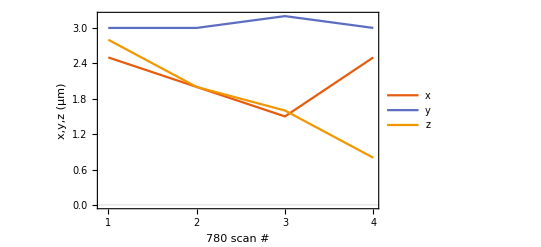

```mathematica
ListPlot[{xCoords,yCoords,zCoords},Joined->True,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"780 scan #","x,y,z (μm)"},PlotLegends->{"x","y","z"},FrameTicks->{Range[4],Automatic}]
```

```mathematica
(*ListPlot[Transpose@{yCoords,zCoords},Joined->True,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"y (μm)","z (μm)"}]
ListPlot[Transpose@{yCoords,xCoords},Joined->True,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"y (μm)","x (μm)"}]
ListPlot[Transpose@{xCoords,zCoords},Joined->True,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"x (μm)","z (μm)"}]*)
```

```mathematica
ListLinePlot3D[Transpose@{xCoords,yCoords,zCoords},PlotRange->All,AxesLabel->{"x (μm)","y (μm)","z (μm)"}]
```

-Graphics3D-

Find the coordinates of the focus for each 852 3D scan.

```mathematica
Date
```

```mathematica
timeStamps852={{},};(*i use the timestamp of the frame closest to being in focus*)
time852abs=Array[AbsoluteTime[timesStamps852[[#]]],Length[timeStamps852]];
```

```mathematica
xstep=0.5;(*um*)
ystep=zstep=0.2(*um*);
xstart={14.17,13.67,14.67,14.67,14.67}-13.67;
timesBtwnScans={};(*in seconds*)
scans3D={
{"852_0-2022-11-01-14-06-xStepSize0.50-yzStepSize0.20-xStart14.17.txt",
"852_1-2022-11-01-14-07-xStepSize0.50-yzStepSize0.20-xStart14.17.txt",
"852_2-2022-11-01-14-08-xStepSize0.50-yzStepSize0.20-xStart14.17.txt",
"852_3-2022-11-01-14-09-xStepSize0.50-yzStepSize0.20-xStart14.17.txt",
"852_4-2022-11-01-14-10-xStepSize0.50-yzStepSize0.20-xStart14.17.txt"},
{"852_0-2022-11-01-14-23-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"852_1-2022-11-01-14-24-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"852_2-2022-11-01-14-25-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"852_3-2022-11-01-14-26-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"852_4-2022-11-01-14-27-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"852_5-2022-11-01-14-28-xStepSize0.50-yzStepSize0.20-xStart13.67.txt",
"852_6-2022-11-01-14-28-xStepSize0.50-yzStepSize0.20-xStart13.67.txt"},
{"852_0-2022-11-01-14-42-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_1-2022-11-01-14-43-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_2-2022-11-01-14-44-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_3-2022-11-01-14-45-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_4-2022-11-01-14-46-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_5-2022-11-01-14-47-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_6-2022-11-01-14-48-xStepSize0.50-yzStepSize0.20-xStart14.67.txt"},
{"852_0-2022-11-01-14-58-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_1-2022-11-01-14-59-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_2-2022-11-01-15-00-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_3-2022-11-01-15-00-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_4-2022-11-01-15-01-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_5-2022-11-01-15-02-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_6-2022-11-01-15-03-xStepSize0.50-yzStepSize0.20-xStart14.67.txt"},
{"852_0-2022-11-01-15-14-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_1-2022-11-01-15-15-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_2-2022-11-01-15-16-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_3-2022-11-01-15-17-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_4-2022-11-01-15-18-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_5-2022-11-01-15-19-xStepSize0.50-yzStepSize0.20-xStart14.67.txt",
"852_6-2022-11-01-15-20-xStepSize0.50-yzStepSize0.20-xStart14.67.txt"}
};
(*the positions of the focus over time*)
yCoords={};
zCoords={};
xCoords={};
tStamps={};
For[i=1,i<Length[scans3D]+1,i++,
slices={};
normslices={};
files=scans3D[[i]];(*a set of transverse scans*)
For[j=1,j<Length[files]+1,j++,
data=Import[files[[j]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
AppendTo[slices,data];
AppendTo[normslices,normdata];
];
{xdim,ydim}=Dimensions[slices[[1]]];
data=slices;
len=Length[data];
Array[(data[[#,3,3;;8]]=1)&,len];
(*"peak value in each frame"*)
maxima=Array[Max[slices[[#]]]&,Length[slices]];
maxIdx=SortBy[Transpose@{Range[len],maxima},#[[2]]&][[-1,1]];
slices-=Min[slices[[maxIdx]]];
slices/=Max[slices[[maxIdx]]];
imageTable=Array[Image[data[[#,;;,;;]]]&,len];Print[GraphicsRow[imageTable]];
unraveled=Flatten[ArrayReshape[slices[[maxIdx]],{1,xdim ydim}]];
maxIdx2D=SortBy[Transpose@{Range[xdim ydim],unraveled},#[[2]]&][[-1,1]];
maxIdxCol=Mod[maxIdx2D,xdim];
maxIdxRow=Floor[maxIdx2D/ydim]+1;
AppendTo[yCoords,maxIdxCol*ystep];
AppendTo[zCoords,maxIdxRow*zstep];
AppendTo[xCoords,maxIdx*xstep+xstart[[i]]];
AppendTo[tStamps,DeltaMins[FileHrMin[files[[maxIdx]]],refTime]];
]
coords852={xCoords,yCoords,zCoords};
times852=tStamps;
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

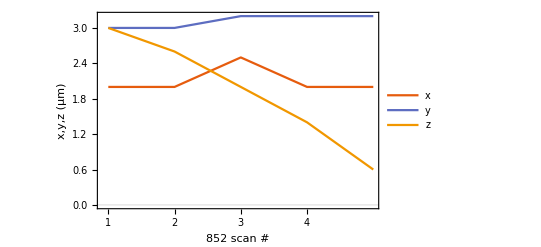

```mathematica
ListPlot[coords852,Joined->True,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"852 scan #","x,y,z (μm)"},PlotLegends->{"x","y","z"},FrameTicks->{Range[4],Automatic}]
```

Compare the drift of the focus for the sets of 780 and 852 3D scans. The order of scans in the lab was 780 scan 1, 852 scan 1, 780 scan 2, 852 scan 2, etc. These plots are versus scan # for the respective wavelength, not versus time. Time stamping

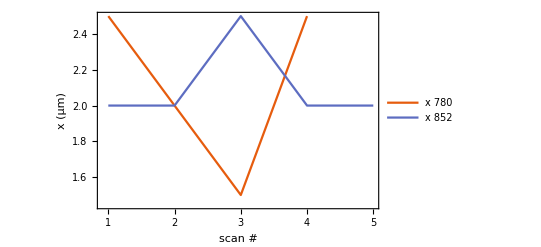

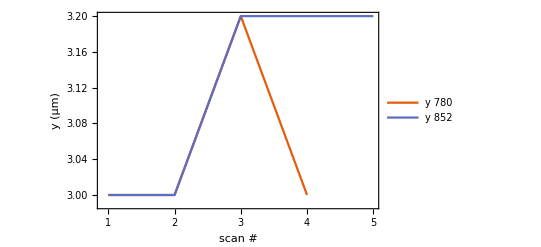

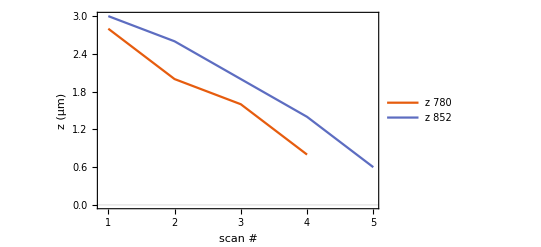

```mathematica
ListPlot[{coords780[[1]],coords852[[1]]},Joined->True,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"scan #","x (μm)"},PlotLegends->{"x 780","x 852"},FrameTicks->{Range[5],Automatic}]
ListPlot[{coords780[[2]],coords852[[2]]},Joined->True,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"scan #","y (μm)"},PlotLegends->{"y 780","y 852"},FrameTicks->{Range[5],Automatic}]
ListPlot[{coords780[[3]],coords852[[3]]},Joined->True,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"scan #","z (μm)"},PlotLegends->{"z 780","z 852"},FrameTicks->{Range[5],Automatic}]
```

Interleave the datasets from the two wavelengths. If the focus for the 780 and 852 coincide and the drift is slow, the focal position of the 852 between two 780 scans should lie between the focus positions for those scans, etc.  It is clear that the primary drift is along the -z direction, that is, downward in the lab frame.  The drift in other directions looks to be fluctuating rather than tending toward a net direction, at least over these 9 scans.

```mathematica
xBoth=Table[If[Mod[(i-1),2]==0,coords852[[1]][[(i+1)/2]],coords780[[1]][[i/2]]],{i,Range[9]}];
yBoth=Table[If[Mod[(i-1),2]==0,coords852[[2]][[(i+1)/2]],coords780[[2]][[i/2]]],{i,Range[9]}];
zBoth=Table[If[Mod[(i-1),2]==0,coords852[[3]][[(i+1)/2]],coords780[[3]][[i/2]]],{i,Range[9]}];
tBoth=Table[If[Mod[(i-1),2]==0,times852[[(i+1)/2]],times780[[i/2]]],{i,Range[9]}];
colors=Table[If[Mod[(i-1),2]==0,Brown,Red],{i,Range[9]}];
```

```mathematica
tBoth
```

{2,11,20,32,38,46,53,61,69}

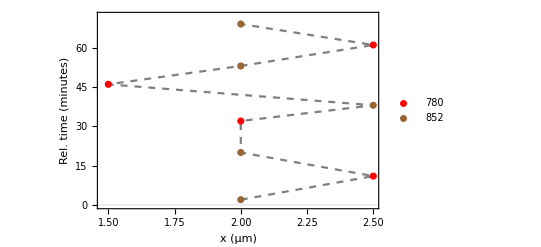

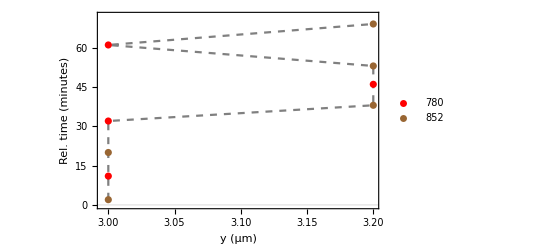

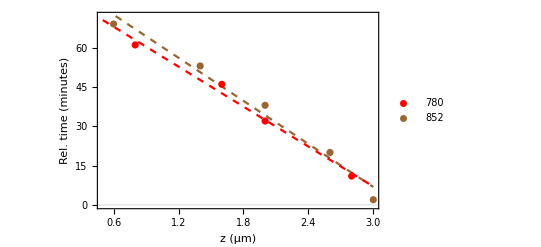

```mathematica
plt1=Show[ListPlot[Transpose@{xBoth,tBoth},PlotTheme->"Scientific",Joined->True,PlotStyle->{Gray,Dashed},FrameLabel->{"x (μm)","Rel. time (minutes)"},LabelStyle->Directive[Black, Medium],PlotRange->{0,72}],ListPlot[Transpose@{coords780[[1]],times780},(*PlotRange->All,*)PlotTheme->"Scientific",PlotLegends->{"780"},PlotStyle->Red],ListPlot[Transpose@{coords852[[1]],times852},(*PlotRange->All,*)PlotTheme->"Scientific",PlotLegends->{"852"},PlotStyle->Brown]]
plt2=Show[ListPlot[Transpose@{yBoth,tBoth},(*PlotRange->All,*)PlotTheme->"Scientific",Joined->True,PlotStyle->{Gray,Dashed},FrameLabel->{"y (μm)","Rel. time (minutes)"},LabelStyle->Directive[Black, Medium],PlotRange->{0,72}],ListPlot[Transpose@{coords780[[2]],times780},(*PlotRange->All,*)PlotTheme->"Scientific",PlotLegends->{"780"},PlotStyle->Red],ListPlot[Transpose@{coords852[[2]],times852},(*PlotRange->All,*)PlotTheme->"Scientific",PlotLegends->{"852"},PlotStyle->Brown]]

z852fit=Fit[Transpose@{coords852[[3]],times852},{1,t},t];
z780fit=Fit[Transpose@{coords780[[3]],times780},{1,t},t];
plt3=Show[(*ListPlot[Transpose@{tBoth,zBoth},PlotRange->All,PlotTheme->"Scientific",Joined->True,PlotStyle->{Gray,Dashed},FrameLabel->{"Rel. time (minutes)","z (μm)"},LabelStyle->Directive[Black, Medium]],*)
Plot[{z852fit,z780fit},{t,0.5,3}(*,PlotRange->Automatic*),PlotTheme->"Scientific",PlotStyle->{Directive[Dashed,Brown],Directive[Dashed,Red]},FrameLabel->{"z (μm)","Rel. time (minutes)"},LabelStyle->Directive[Black, Medium],PlotRange->{0,72}],
ListPlot[Transpose@{coords780[[3]],times780},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"780"},PlotStyle->Red],ListPlot[Transpose@{coords852[[3]],times852},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"852"},PlotStyle->Brown]]
```

```mathematica
Export["fiberscan_852_780_xdrift.svg",plt1]
Export["fiberscan_852_780_ydrift.svg",plt2]
Export["fiberscan_852_780_zdrift.svg",plt3]
```

fiberscan_852_780_xdrift.svg

fiberscan_852_780_ydrift.svg

fiberscan_852_780_zdrift.svg

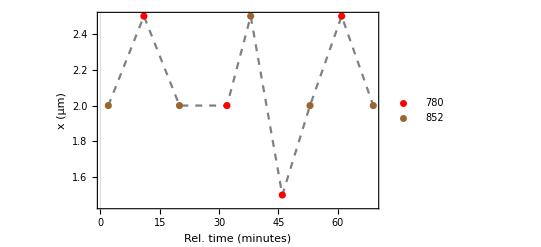

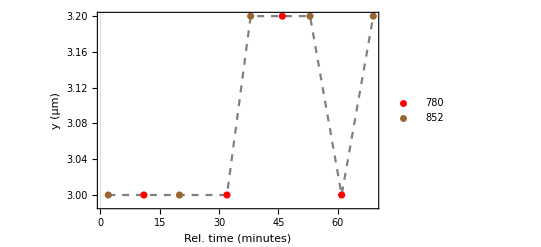

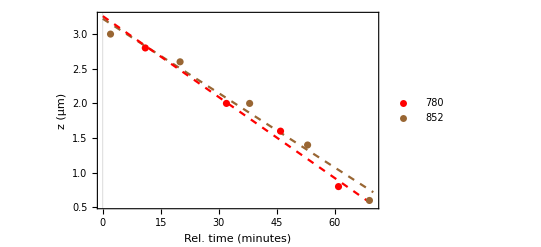

```mathematica
plt1=Show[ListPlot[Transpose@{tBoth,xBoth},PlotRange->All,PlotTheme->"Scientific",Joined->True,PlotStyle->{Gray,Dashed},FrameLabel->{"Rel. time (minutes)","x (μm)"},LabelStyle->Directive[Black, Medium]],ListPlot[Transpose@{times780,coords780[[1]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"780"},PlotStyle->Red],ListPlot[Transpose@{times852,coords852[[1]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"852"},PlotStyle->Brown]]
plt2=Show[ListPlot[Transpose@{tBoth,yBoth},PlotRange->All,PlotTheme->"Scientific",Joined->True,PlotStyle->{Gray,Dashed},FrameLabel->{"Rel. time (minutes)","y (μm)"},LabelStyle->Directive[Black, Medium]],ListPlot[Transpose@{times780,coords780[[2]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"780"},PlotStyle->Red],ListPlot[Transpose@{times852,coords852[[2]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"852"},PlotStyle->Brown]]

z852fit=Fit[Transpose@{times852,coords852[[3]]},{1,t},t];
z780fit=Fit[Transpose@{times780,coords780[[3]]},{1,t},t];
plt3=Show[(*ListPlot[Transpose@{tBoth,zBoth},PlotRange->All,PlotTheme->"Scientific",Joined->True,PlotStyle->{Gray,Dashed},FrameLabel->{"Rel. time (minutes)","z (μm)"},LabelStyle->Directive[Black, Medium]],*)
Plot[{z852fit,z780fit},{t,0,70},PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Directive[Dashed,Brown],Directive[Dashed,Red]},FrameLabel->{"Rel. time (minutes)","z (μm)"},LabelStyle->Directive[Black, Medium]],
ListPlot[Transpose@{times780,coords780[[3]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"780"},PlotStyle->Red],ListPlot[Transpose@{times852,coords852[[3]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"852"},PlotStyle->Brown]]
```

```mathematica
Integrate[(z852fit-z780fit),{t,0,70}]/70(*the average difference between the fitted lines for the drift in z*)
```

0.0727681

```mathematica
(*Export["fiberscan_852_780_xdrift.svg",plt1]
Export["fiberscan_852_780_ydrift.svg",plt2]
Export["fiberscan_852_780_zdrift.svg",plt3]*)
```

fiberscan_852_780_xdrift.svg

fiberscan_852_780_ydrift.svg

fiberscan_852_780_zdrift.svg

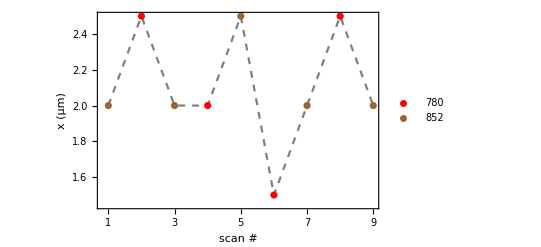

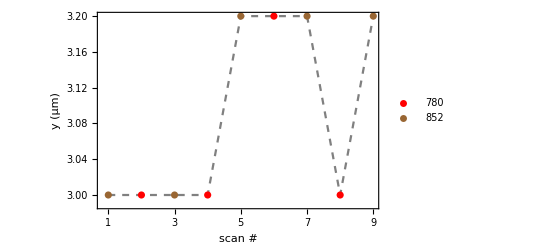

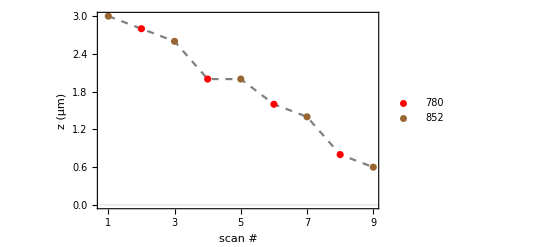

```mathematica
Show[ListPlot[xBoth,PlotRange->All,PlotTheme->"Scientific",Joined->True,FrameTicks->{Range[9],Automatic},PlotStyle->{Gray,Dashed},FrameLabel->{"scan #","x (μm)"}],ListPlot[Transpose@{{2,4,6,8},coords780[[1]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"780"},FrameTicks->{Range[9],Automatic},PlotStyle->Red],ListPlot[Transpose@{{1,3,5,7,9},coords852[[1]]},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"scan #","x (μm)"},PlotLegends->{"852"},FrameTicks->{Range[9],Automatic},PlotStyle->Brown]]
Show[ListPlot[yBoth,PlotRange->All,PlotTheme->"Scientific",Joined->True,FrameTicks->{Range[9],Automatic},PlotStyle->{Gray,Dashed},FrameLabel->{"scan #","y (μm)"}],ListPlot[Transpose@{{2,4,6,8},coords780[[2]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"780"},FrameTicks->{Range[9],Automatic},PlotStyle->Red],ListPlot[Transpose@{{1,3,5,7,9},coords852[[2]]},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"scan #","y (μm)"},PlotLegends->{"852"},FrameTicks->{Range[9],Automatic},PlotStyle->Brown]]
Show[ListPlot[zBoth,PlotRange->All,PlotTheme->"Scientific",Joined->True,FrameTicks->{Range[9],Automatic},PlotStyle->{Gray,Dashed},FrameLabel->{"scan #","z (μm)"}],ListPlot[Transpose@{{2,4,6,8},coords780[[3]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"780"},FrameTicks->{Range[9],Automatic},PlotStyle->Red],ListPlot[Transpose@{{1,3,5,7,9},coords852[[3]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"852"},FrameTicks->{Range[9],Automatic},PlotStyle->Brown]
]
```

```mathematica
zBoth
```

{3.,2.8,2.6,2.,2.,1.6,1.4,0.8,0.6}

Now include timestamps and fit the z coordinates (down in the lab frame) to that. This gives the transverse alignment of the two focal spots in the z direction. In y, the separation is probably less than 200 nm but this is the resolution limit of the scan. A more precise method of determining the localization in y and x would be to do Gaussian fits and find the center coordinate.

```mathematica
timeStamps
Show[ListPlot[zBoth,PlotRange->All,PlotTheme->"Scientific",Joined->True,FrameTicks->{Range[9],Automatic},PlotStyle->{Gray,Dashed},FrameLabel->{"scan #","z (μm)"}],ListPlot[Transpose@{{2,4,6,8},coords780[[3]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"780"},FrameTicks->{Range[9],Automatic},PlotStyle->Red],ListPlot[Transpose@{{1,3,5,7,9},coords852[[3]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{"852"},FrameTicks->{Range[9],Automatic},PlotStyle->Brown]
]
```

### Low-res large range 3D scans, one for each wavelength

780 scan with yz slices at different x positions along the optical axis. The apparent angle of the beam likely arises in part from an angle between the axis of the mirror and the x axis of the NanoMax.

```mathematica
files={
"780_0-2022-11-01-16-55-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_1-2022-11-01-16-56-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_2-2022-11-01-16-57-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_3-2022-11-01-16-58-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_4-2022-11-01-16-59-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_5-2022-11-01-17-01-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_6-2022-11-01-17-02-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_7-2022-11-01-17-03-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_8-2022-11-01-17-04-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_9-2022-11-01-17-05-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"780_10-2022-11-01-17-06-xStepSize1.00-yzStepSize0.30-xStart9.97.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
maxima=Array[Max[slices[[#]]]&,Length[slices]];
maxIdx=SortBy[Transpose@{Range[len],maxima},#[[2]]&][[-1,1]];
slices-=Min[slices[[maxIdx]]];
slices/=Max[slices[[maxIdx]]];
{xdim,ydim}=Dimensions[slices[[1]]]
data=slices;
len=Length[data];
Array[(data[[#,3,3;;8]]=1)&,len];
imageTable=Array[Image[data[[#,;;,;;]]]&,len];
GraphicsRow[imageTable]
"peak value in each frame"
Array[Max[slices[[#]]]&,Length[slices]]
```

{34,34}

-Graphics-

peak value in each frame

{0.133824,0.169971,0.285609,0.468282,0.744317,1.,0.908306,0.563959,0.396548,0.30916,0.231683}

```mathematica
files={
"852_0-2022-11-01-16-41-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_1-2022-11-01-16-43-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_2-2022-11-01-16-44-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_3-2022-11-01-16-45-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_4-2022-11-01-16-46-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_5-2022-11-01-16-47-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_6-2022-11-01-16-48-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_7-2022-11-01-16-49-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_8-2022-11-01-16-51-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_9-2022-11-01-16-52-xStepSize1.00-yzStepSize0.30-xStart9.97.txt",
"852_10-2022-11-01-16-53-xStepSize1.00-yzStepSize0.30-xStart9.97.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
len=Length[slices];
maxima=Array[Max[slices[[#]]]&,len];
maxIdx=SortBy[Transpose@{Range[len],maxima},#[[2]]&][[-1,1]];
slices-=Min[slices[[maxIdx]]];
slices/=Max[slices[[maxIdx]]];
{xdim,ydim}=Dimensions[slices[[1]]]
data=slices;
len=Length[data];
Array[(data[[#,3,3;;8]]=1)&,len];
imageTable=Array[Image[data[[#,;;,;;]]]&,len];
GraphicsRow[imageTable]
"peak value in each frame"
Array[Max[slices[[#]]]&,Length[slices]]
```

{34,34}

-Graphics-

peak value in each frame

{0.152949,0.186284,0.335494,0.533922,0.937237,1.,0.80473,0.500706,0.337013,0.23796,0.177487}

## 2022.10.22

a 3D transverse scan (y,z then x) after gluing the fiber launcher (i.e. everything is now glued)

```mathematica
files={
"19-2022-10-22-20-21-xStepSize0.50-yzStepSize0.20.txt",
"18-2022-10-22-20-20-xStepSize0.50-yzStepSize0.20.txt",
"17-2022-10-22-20-20-xStepSize0.50-yzStepSize0.20.txt",
"16-2022-10-22-20-19-xStepSize0.50-yzStepSize0.20.txt",
"15-2022-10-22-20-18-xStepSize0.50-yzStepSize0.20.txt",
"14-2022-10-22-20-17-xStepSize0.50-yzStepSize0.20.txt",
"13-2022-10-22-20-16-xStepSize0.50-yzStepSize0.20.txt",
"12-2022-10-22-20-15-xStepSize0.50-yzStepSize0.20.txt",
"11-2022-10-22-20-14-xStepSize0.50-yzStepSize0.20.txt",
"10-2022-10-22-20-13-xStepSize0.50-yzStepSize0.20.txt",
"9-2022-10-22-20-12-xStepSize0.50-yzStepSize0.20.txt",
"8-2022-10-22-20-11-xStepSize0.50-yzStepSize0.20.txt",
"7-2022-10-22-20-10-xStepSize0.50-yzStepSize0.20.txt",
"6-2022-10-22-20-09-xStepSize0.50-yzStepSize0.20.txt",
"5-2022-10-22-20-08-xStepSize0.50-yzStepSize0.20.txt",
"4-2022-10-22-20-07-xStepSize0.50-yzStepSize0.20.txt",
"3-2022-10-22-20-06-xStepSize0.50-yzStepSize0.20.txt",
"2-2022-10-22-20-05-xStepSize0.50-yzStepSize0.20.txt",
"1-2022-10-22-20-04-xStepSize0.50-yzStepSize0.20.txt",
"0-2022-10-22-20-03-xStepSize0.50-yzStepSize0.20.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
slices-=Min[slices[[11]]];
slices/=Max[slices[[11]]];
```

```mathematica
dims={2,Length[normslices]/2,31,31};
reshaped=ArrayReshape[normslices,dims];
Array[(reshaped[[#1,#2,3,3;;8]]=1)&,dims[[1;;2]]];
imageTable=Array[Colorize[Image[reshaped[[#1,#2,;;,;;]]],ColorFunction->ColorData["CherryTones"]]&,dims[[1;;2]]];
plt=GraphicsGrid[imageTable,ImageSize->Large]
```

-Graphics-

```mathematica
Export["fiber_scan_tranverse_slices.pdf",plt]
```

fiber_scan_tranverse_slices.pdf

```mathematica
focus=slices[[11]];
focus[[3,3;;8]]=1;
Colorize[Image[focus],ColorFunction->ColorData["CherryTones"]]
```

-Graphics-

```mathematica
{xdim,ydim}=Dimensions[data]
```

{31,31}

```mathematica
ListPlot3D[slices[[11]],PlotRange->All]
```

-Graphics3D-

{w→0.777844,x0→2.98054}

{w→0.664885,x0→3.35525}

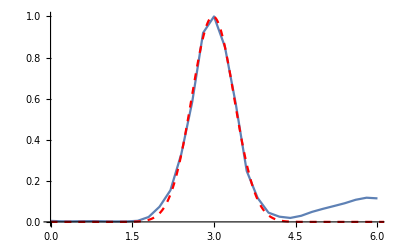

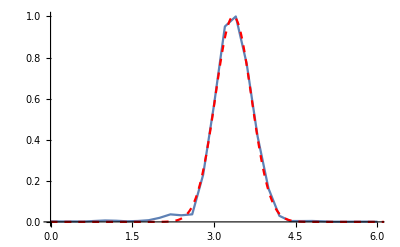

```mathematica
xdata=Transpose@{Range[0,(xdim-1)*0.2,0.2],focus[[18,;;]]};
ydata=Transpose@{Range[0,(ydim-1)*0.2,0.2],focus[[;;,16]]};
model=Exp[-(2(x-x0)^2)/w^2];
xfit=FindFit[xdata,model,{{w,0.6},{x0,3}},x]
yfit=FindFit[ydata,model,{{w,0.6},{x0,3.5}},x]
Show[ListPlot[xdata,PlotRange->All,Joined->True(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],
Plot[model/.xfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
Show[ListPlot[ydata,PlotRange->All,Joined->True(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],Plot[model/.yfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
```

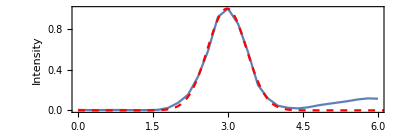

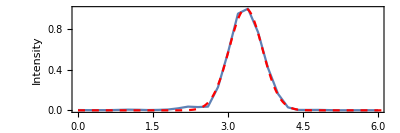

```mathematica
Show[ListPlot[xdata,PlotRange->All,Joined->True,Axes->False, Frame->{True,True,False,False},FrameLabel->{"x (μm)","Intensity"},LabelStyle->Directive[Black, FontSize->14],AspectRatio->1/3(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],
Plot[model/.xfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
Show[ListPlot[ydata,PlotRange->All,Joined->True,Axes->False, Frame->{True,True,False,False},FrameLabel->{"x (μm)","Intensity"},LabelStyle->Directive[Black, FontSize->14],AspectRatio->1/3(*,PlotTheme->"Scientific",FrameLabel->{"μm"}*)],Plot[model/.yfit,{x,0,10},PlotRange->All,PlotStyle->{Dashed,Red}]]
```

The focus and two scans defocused by +/-5um to see how the beam moves in the transverse plane as it expands.

```mathematica
files={
"2-2022-10-22-16-35-xStepSize5.00-yzStepSize0.20.txt",
"1-2022-10-22-16-34-xStepSize5.00-yzStepSize0.20.txt",
"0-2022-10-22-16-34-xStepSize5.00-yzStepSize0.20.txt"
};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
```

```mathematica
slices-=Min[slices[[2]]];
slices/=Max[slices[[2]]];
```

```mathematica
Image[normslices[[1]],ImageSize->Small]
Image[normslices[[2]],ImageSize->Small]
Image[normslices[[3]],ImageSize->Small]
```

-Graphics-

-Graphics-

-Graphics-

This is in focus as checked by playing with the x axis knob. The previous data is very close to focus, but off by 0.8 um.

```mathematica
data=Import["focal_spot_1615_20221022.txt","Table"];
data-=Min[data];
data/=Max[data];
Image[data]
ListPlot3D[data,PlotRange->All]
```

-Graphics-

-Graphics3D-

```mathematica
{xdim,ydim}=Dimensions[data]
```

{51,51}

{w→0.852815,x0→4.73522}

{w→0.671164,x0→5.46727}

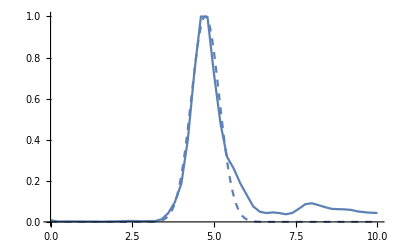

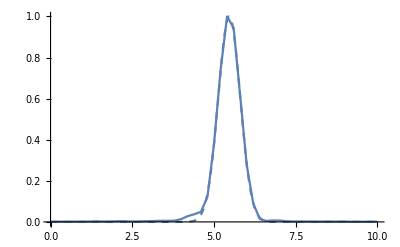

```mathematica
xdata=Transpose@{Range[0,(xdim-1)*0.2,0.2],data[[28,;;]]};
ydata=Transpose@{Range[0,(ydim-1)*0.2,0.2],data[[;;,24]]};
model=Exp[-(2(x-x0)^2)/w^2];
xfit=FindFit[xdata,model,{{w,0.6},{x0,5}},x]
yfit=FindFit[ydata,model,{{w,0.6},{x0,5}},x]
Show[ListPlot[xdata,PlotRange->All,Joined->True],
Plot[model/.xfit,{x,0,10},PlotRange->All,PlotStyle->Dashed]]
Show[ListPlot[ydata,PlotRange->All,Joined->True],Plot[model/.yfit,{x,0,10},PlotRange->All,PlotStyle->Dashed]]
```

I think the 3d scan set below this is out of focus. I also tuned the fiber launcher alignment somewhat because the out of focus field seemed asymmetric.

```mathematica
data=Import["focal_spot_1554_20221022.txt","Table"];
data-=Min[data];
data/=Max[data];
Image[data]
ListPlot3D[data,PlotRange->All]
```

-Graphics-

-Graphics3D-

```mathematica
{xdim,ydim}=Dimensions[data]
```

{51,51}

{w→0.884303,x0→4.93235}

{w→0.737264,x0→5.34028}

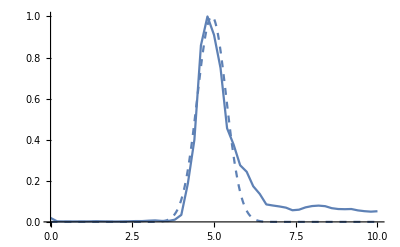

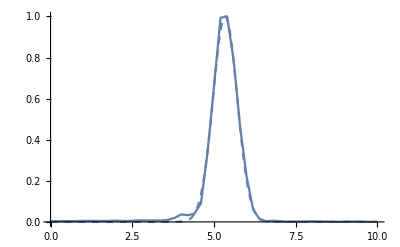

```mathematica
xdata=Transpose@{Range[0,(xdim-1)*0.2,0.2],data[[28,;;]]};
ydata=Transpose@{Range[0,(ydim-1)*0.2,0.2],data[[;;,25]]};
model=Exp[-(2(x-x0)^2)/w^2];
xfit=FindFit[xdata,model,{{w,0.6},{x0,5}},x]
yfit=FindFit[ydata,model,{{w,0.6},{x0,5}},x]
Show[ListPlot[xdata,PlotRange->All,Joined->True],
Plot[model/.xfit,{x,0,10},PlotRange->All,PlotStyle->Dashed]]
Show[ListPlot[ydata,PlotRange->All,Joined->True],Plot[model/.yfit,{x,0,10},PlotRange->All,PlotStyle->Dashed]]
```

Last night’s scan failed due to communication issues with the piezo controller. Power cycling solved the issue. Here are transverse scans from today at different axial locations, after having glued (and curing the glue) the doublet lens and parabolic mirror last night.

```mathematica
files={
"7-2022-10-22-12-53-xStepSize0.50-yzStepSize0.20.txt",
"6-2022-10-22-12-42-xStepSize0.50-yzStepSize0.20.txt",
"5-2022-10-22-12-30-xStepSize0.50-yzStepSize0.20.txt",
"4-2022-10-22-12-19-xStepSize0.50-yzStepSize0.20.txt",
"3-2022-10-22-12-08-xStepSize0.50-yzStepSize0.20.txt",
"2-2022-10-22-11-57-xStepSize0.50-yzStepSize0.20.txt",
"1-2022-10-22-11-46-xStepSize0.50-yzStepSize0.20.txt",
"0-2022-10-22-11-34-xStepSize0.50-yzStepSize0.20.txt"};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
```

```mathematica
data//Dimensions
```

{76,76}

```mathematica
dims={2,Length[normslices]/2,76,76};
reshaped=ArrayReshape[normslices,dims];
Array[(reshaped[[#1,#2,3,3;;8]]=1)&,dims[[1;;2]]];
imageTable=Array[Image[reshaped[[#1,#2,;;,;;]]]&,dims[[1;;2]]];
GraphicsGrid[imageTable]
```

-Graphics-

```mathematica
norm=Max[slices[[1]]-Min[slices[[1]]]];
min=Min[slices[[1]]];
GraphicsGrid[{Array[ListPlot3D[(slices[[#]]-min)/norm,PlotRange->{0,1},Axes->False]&,Length[normslices]]}]
```

-Graphics-

```mathematica
i=4;
focus=(slices[[i]]-Min[slices[[i]]])/(Max[slices[[i]]]-Min[slices[[i]]]);
ListPlot3D[(slices[[i]]-Min[slices[[i]]])/(Max[slices[[i]]]-Min[slices[[i]]]),PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Image[focus]
```

-Graphics-

```mathematica
Length[Range[0,75*0.2,0.2]]
```

76

```mathematica
focus[[;;,31]]//Length
focus[[;;,31]]//Length
```

76

76

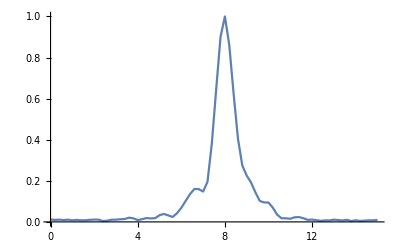

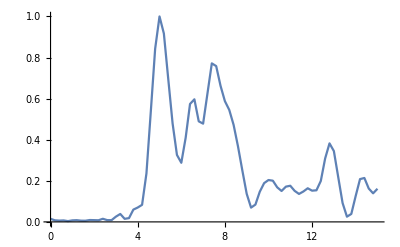

```mathematica
ListPlot[Transpose@@{{Range[0,75*0.2,0.2],focus[[;;,26]]}},Joined->True,PlotRange->All]
ListPlot[Transpose@@{{Range[0,75*0.2,0.2],focus[[41,;;]]}},Joined->True,PlotRange->All]
```

## 2022.10.21

Transverse scans at different axial locations after gluing (and curing the glue) the doublet lens and parabolic mirror.

```mathematica
files={
"19-2022-10-22-00-05-xStepSize0.50-yzStepSize0.20.txt",
"18-2022-10-22-00-01-xStepSize0.50-yzStepSize0.20.txt",
"17-2022-10-21-23-56-xStepSize0.50-yzStepSize0.20.txt",
"16-2022-10-21-23-52-xStepSize0.50-yzStepSize0.20.txt",
"15-2022-10-21-23-47-xStepSize0.50-yzStepSize0.20.txt",
"14-2022-10-21-23-43-xStepSize0.50-yzStepSize0.20.txt",
"13-2022-10-21-23-38-xStepSize0.50-yzStepSize0.20.txt",
"12-2022-10-21-23-34-xStepSize0.50-yzStepSize0.20.txt",
"11-2022-10-21-23-29-xStepSize0.50-yzStepSize0.20.txt",
"10-2022-10-21-23-25-xStepSize0.50-yzStepSize0.20.txt",
"9-2022-10-21-23-20-xStepSize0.50-yzStepSize0.20.txt",
"8-2022-10-21-23-16-xStepSize0.50-yzStepSize0.20.txt",
"7-2022-10-21-23-12-xStepSize0.50-yzStepSize0.20.txt",
"6-2022-10-21-23-07-xStepSize0.50-yzStepSize0.20.txt",
"5-2022-10-21-23-03-xStepSize0.50-yzStepSize0.20.txt",
"4-2022-10-21-22-58-xStepSize0.50-yzStepSize0.20.txt",
"3-2022-10-21-22-54-xStepSize0.50-yzStepSize0.20.txt",
"2-2022-10-21-22-49-xStepSize0.50-yzStepSize0.20.txt",
"1-2022-10-21-22-45-xStepSize0.50-yzStepSize0.20.txt",
"0-2022-10-21-22-40-xStepSize0.50-yzStepSize0.20.txt"};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
```

```mathematica
data//Dimensions
```

{96,96}

```mathematica
dims={2,Length[normslices]/2,96,96};
reshaped=ArrayReshape[normslices,dims];
Array[(reshaped[[#1,#2,3,3;;8]]=1)&,dims[[1;;2]]];
imageTable=Array[Image[reshaped[[#1,#2,;;,;;]]]&,dims[[1;;2]]];
GraphicsGrid[imageTable]
```

-Graphics-

```mathematica
norm=Max[slices[[1]]-Min[slices[[1]]]];
min=Min[slices[[1]]];
GraphicsGrid[{Array[ListPlot3D[(slices[[#]]-min)/norm,PlotRange->{0,1},Axes->False]&,Length[normslices]]}]
```

-Graphics-

```mathematica
focus=(slices[[10]]-Min[slices[[10]]])/(Max[slices[[10]]]-Min[slices[[10]]]);
ListPlot3D[(slices[[10]]-Min[slices[[10]]])/(Max[slices[[10]]]-Min[slices[[10]]]),PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Image[focus]
```

-Graphics-

```mathematica
Length[Range[0,50*0.2,0.2]]
```

51

```mathematica
focus[[;;,31]]//Length
focus[[;;,31]]//Length
```

51

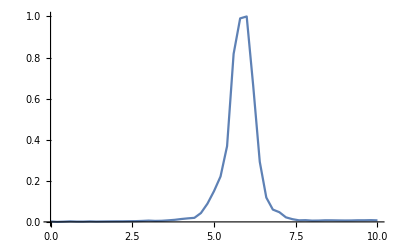

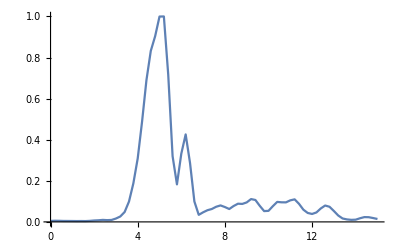

```mathematica
ListPlot[Transpose@@{{Range[0,50*0.2,0.2],focus[[;;,27]]}},Joined->True,PlotRange->All]
ListPlot[Transpose@@{{Range[0,75*0.2,0.2],focus[[31,;;]]}},Joined->True,PlotRange->All]
```

Transverse scans at different axial locations before gluing any of the components in the Macor tube.

```mathematica
files={
"23-2022-10-21-16-57-xStepSize0.50-yzStepSize0.20.txt",
"22-2022-10-21-16-50-xStepSize0.50-yzStepSize0.20.txt",
"21-2022-10-21-16-43-xStepSize0.50-yzStepSize0.20.txt",
"20-2022-10-21-16-36-xStepSize0.50-yzStepSize0.20.txt",
"19-2022-10-21-16-30-xStepSize0.50-yzStepSize0.20.txt",
"18-2022-10-21-16-23-xStepSize0.50-yzStepSize0.20.txt",
"17-2022-10-21-16-16-xStepSize0.50-yzStepSize0.20.txt",
"16-2022-10-21-16-09-xStepSize0.50-yzStepSize0.20.txt",
"15-2022-10-21-16-02-xStepSize0.50-yzStepSize0.20.txt",
"14-2022-10-21-15-55-xStepSize0.50-yzStepSize0.20.txt",
"13-2022-10-21-15-48-xStepSize0.50-yzStepSize0.20.txt",
"12-2022-10-21-15-41-xStepSize0.50-yzStepSize0.20.txt",
"11-2022-10-21-15-35-xStepSize0.50-yzStepSize0.20.txt",
"10-2022-10-21-15-28-xStepSize0.50-yzStepSize0.20.txt",
"9-2022-10-21-15-21-xStepSize0.50-yzStepSize0.20.txt",
"8-2022-10-21-15-14-xStepSize0.50-yzStepSize0.20.txt",
"7-2022-10-21-15-07-xStepSize0.50-yzStepSize0.20.txt",
"6-2022-10-21-15-00-xStepSize0.50-yzStepSize0.20.txt",
"5-2022-10-21-14-53-xStepSize0.50-yzStepSize0.20.txt",
"4-2022-10-21-14-46-xStepSize0.50-yzStepSize0.20.txt",
"3-2022-10-21-14-39-xStepSize0.50-yzStepSize0.20.txt",
"2-2022-10-21-14-33-xStepSize0.50-yzStepSize0.20.txt",
"1-2022-10-21-14-26-xStepSize0.50-yzStepSize0.20.txt",
"0-2022-10-21-14-19-xStepSize0.50-yzStepSize0.20.txt"};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
```

```mathematica
data//Dimensions
```

{51,76}

```mathematica
dims={2,Length[normslices]/2,51,76};
reshaped=ArrayReshape[normslices,dims];
Array[(reshaped[[#1,#2,3,3;;8]]=1)&,dims[[1;;2]]];
imageTable=Array[Image[reshaped[[#1,#2,;;,;;]]]&,dims[[1;;2]]];
GraphicsGrid[imageTable]
```

-Graphics-

```mathematica
norm=Max[slices[[1]]-Min[slices[[1]]]];
min=Min[slices[[1]]];
GraphicsGrid[{Array[ListPlot3D[(slices[[#]]-min)/norm,PlotRange->{0,1},Axes->False]&,Length[normslices]]}]
```

-Graphics-

```mathematica
focus=(slices[[10]]-Min[slices[[10]]])/(Max[slices[[10]]]-Min[slices[[10]]]);
ListPlot3D[(slices[[10]]-Min[slices[[10]]])/(Max[slices[[10]]]-Min[slices[[10]]]),PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Image[focus]
```

-Graphics-

```mathematica
Length[Range[0,50*0.2,0.2]]
```

51

```mathematica
focus[[;;,31]]//Length
focus[[;;,31]]//Length
```

51

```mathematica
ListPlot[Transpose@@{{Range[0,50*0.2,0.2],focus[[;;,27]]}},Joined->True,PlotRange->All]
ListPlot[Transpose@@{{Range[0,75*0.2,0.2],focus[[31,;;]]}},Joined->True,PlotRange->All]
```

-Graphics-

-Graphics-

## 2022.10.20

Transverse scans at different axial locations.

```mathematica
files={
"slice_10um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_10pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt","slice_11um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_11pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_12um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_12pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt","slice_13um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_13pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_14um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_14pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt","slice_15um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_15pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_16um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_16pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt","slice_17um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_17pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_18um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt","slice_18pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_19um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt",
"slice_19pt5um_axial_100ms_delay_pt2um_res_0to29x0to29_20221020.txt"};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
```

```mathematica
(*For[i=1,i<Length[files],i++,
xslice=ListPlot[slices[[i,74]],Joined->True,PlotRange->{-0.04,.4}];
yslice=ListPlot[slices[[i,;;,84]],Joined->True,PlotRange->{-0.04,.4}];
Print[GraphicsGrid[{{xslice,yslice}}]];
]*)
```

```mathematica
dims={2,Length[normslices]/2,51,51};
reshaped=ArrayReshape[normslices,dims];
Array[(reshaped[[#1,#2,3,3;;8]]=1)&,dims[[1;;2]]];
imageTable=Array[Image[reshaped[[#1,#2,;;,;;]]]&,dims[[1;;2]]];
```

```mathematica
GraphicsGrid[imageTable]
```

-Graphics-

```mathematica
ims={2,Length[slices]/2,51,51};
reshaped=ArrayReshape[slices,dims];
imageTable=Array[Image[reshaped[[#1,#2,;;,;;]]]&,dims[[1;;2]]];
GraphicsGrid[imageTable]
```

-Graphics-

## 2022.10.14

General::munfl: Exp[-4499.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12798.7] is too small to represent as a normalized machine number; precision may be lost.

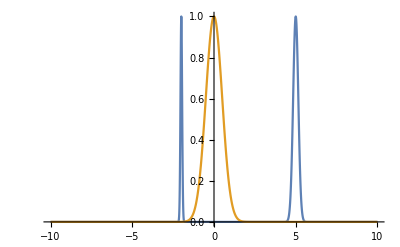

General::munfl: Exp[-4499.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12798.7] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

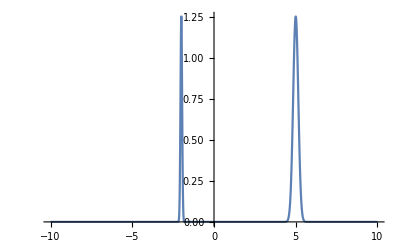

```mathematica
detector=Exp[-2(x+2)^2/0.01]+Exp[-2(x-5)^2/0.1];
signal=Exp[-2 x^2/1];
Plot[{detector,signal},{x,-10,10},PlotRange->All]
Plot[NIntegrate[(detector/.x->t)( signal/.x->t-τ),{τ,-10,10}],{t,-10,10},PlotRange->All]
(*Integrate[*)
```

## 2022.10.13

Transverse scans at different axial locations.

```mathematica
files={"slice_15um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt","slice_16um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt","slice_17um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt","slice_18um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt","slice_19um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt"};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
(*Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];*)
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
```

```mathematica
GraphicsGrid[{Array[Image[normslices[[#]]]&,Length[normslices]]}]
```

-Graphics-

```mathematica
files={"slice_15um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt","slice_16um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt","slice_17um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt","slice_18um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt","slice_19um_axial_100ms_delay_pt2um_res_0to29x0to29_20221013.txt"};
slices={};
normslices={};
For[i=1,i<Length[files]+1,i++,
data=Import[files[[i]],"Table"];
normdata=data;
normdata-=Min[normdata];
normdata/=Max[normdata];
Print[Image[normdata]];
Print[ListPlot3D[normdata,PlotRange->All]];
AppendTo[slices,data];
AppendTo[normslices,normdata];
]
```

-Graphics-

-Graphics3D-

-Graphics-

-Graphics3D-

-Graphics-

-Graphics3D-

-Graphics-

-Graphics3D-

-Graphics-

-Graphics3D-

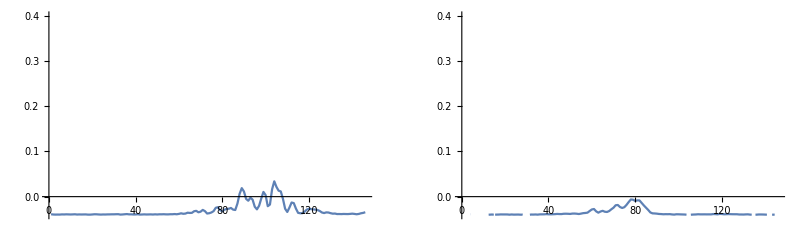

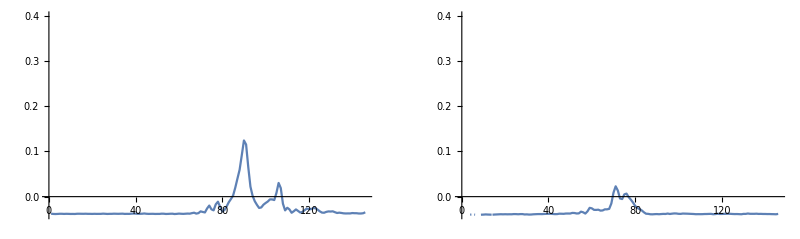

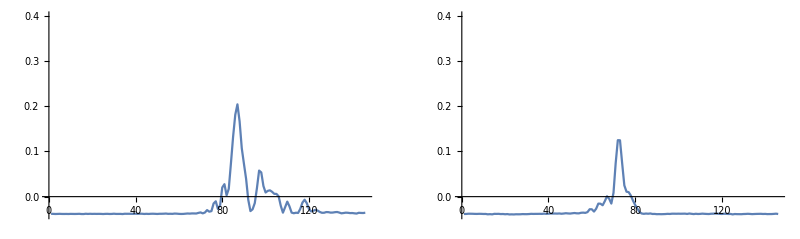

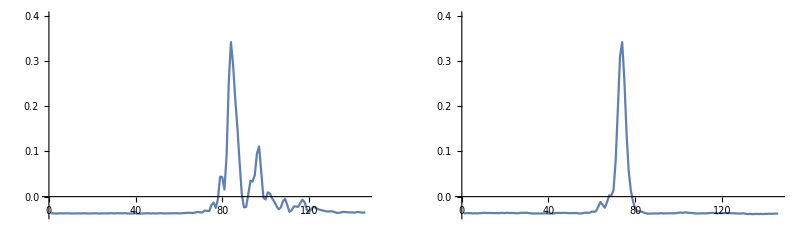

```mathematica
For[i=1,i<Length[files],i++,
xslice=ListPlot[slices[[i,74]],Joined->True,PlotRange->{-0.04,.4}];
yslice=ListPlot[slices[[i,;;,84]],Joined->True,PlotRange->{-0.04,.4}];
Print[GraphicsGrid[{{xslice,yslice}}]];
]
```